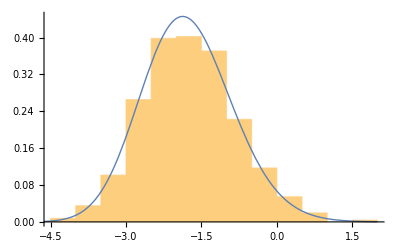

```mathematica
Clear["Global`*"]
n=1000;
le=RandomVariate[MatrixPropertyDistribution[(Max[Eigenvalues[x]]-Sqrt[4. n]) n^(1./6),x\[Distributed]GaussianUnitaryMatrixDistribution[n]],512];
Show[Histogram[le,Automatic,PDF],Plot[PDF[TracyWidomDistribution[2],x],{x,-5,2},PlotStyle->Thick]]
```

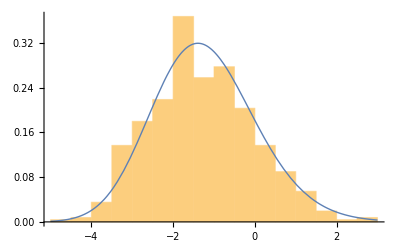

```mathematica
Clear["Global`*"]
n=1000;
le=RandomVariate[MatrixPropertyDistribution[(Max[Eigenvalues[x]]-Sqrt[2 n]) Sqrt[2]n^(1./6),x\[Distributed]GaussianOrthogonalMatrixDistribution[n]],512];
Show[Histogram[le,Automatic,PDF],Plot[PDF[TracyWidomDistribution[1],x],{x,-5,3},PlotStyle->Thick]]
```

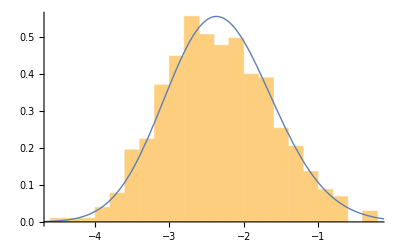

```mathematica
Clear["Global`*"]
n=1000;
le=RandomVariate[MatrixPropertyDistribution[(Max[Eigenvalues[x]]-2Sqrt[2 n])(n/4)^(1./6),x\[Distributed]GaussianSymplecticMatrixDistribution[n]],512];
Show[Histogram[le,Automatic,PDF],Plot[PDF[TracyWidomDistribution[4],x],{x,-5,1},PlotStyle->Thick]]
```